# Extended Stochastic Many-Body Transport Toy Model for HgCdTe NIR Detector Pixels

This notebook instantiates a Hubbard/Anderson-inspired stochastic transport model. Holes move on a 3D lattice, interact with dynamically occupied defect orbitals, and collect at p+ anodes. The local effective Hamiltonian changes as holes are trapped, emitted, recombined, or collected.

## 1. Clear State and Global Parameters

```mathematica
ClearAll["Global`*"];
```

```mathematica
SeedRandom[12345];

(* Geometry in microns. The volume is a small 3 x 3 anode supercell. *)
pixelPitchUm = 10.0;
numberOfPixelsX = 3;
numberOfPixelsY = 3;
depletionThicknessUm = 5.0;
latticeSpacingUm = 0.1;

xCoordinatesUm = Range[0, numberOfPixelsX pixelPitchUm, latticeSpacingUm];
yCoordinatesUm = Range[0, numberOfPixelsY pixelPitchUm, latticeSpacingUm];
zCoordinatesUm = Range[0, depletionThicknessUm, latticeSpacingUm];

(* Thermal and stochastic model parameters. Energies are toy eV values. *)
temperatureK = 89.0;
boltzmannEVperK = 8.617333262*10^-5;
thermalEnergyEV = boltzmannEVperK temperatureK

numberOfMobileHoles = 90;
numberOfTransportSteps = 800;
initialHoleZRangeUm = {0.0, 1.0};
collectionRadiusUm = 2.75;
softeningLengthUm = 0.65;

(* Hamiltonian-like energy scales. Parameters not accurate to reality, afaik *)
anodeAttractionEV = 0.3;
collectedChargeRepulsionEV = 0.010;
defectCoulombAmplitudeEV = 0.050;
defectCaptureBaseProbability = 0.10;
defectEmissionBaseProbability = 0.025;
defectRecombinationProbability = 10^-4;
nearestNeighborHoppingTemperatureFactor = 1.0;

(* Drift field, taken form Mosby et al 2020 *)
driftFieldVperCm = 20.0;
driftFieldVperUm=driftFieldVperCm*10^-4;
driftEnergyAcrossAbsorberEV=driftFieldVperUm*depletionThicknessUm
(*Hole drift energy contribution.Negative sign means larger z is energetically favorable for holes,i.e.drift toward the anode plane at z=d.*)
holeDriftEnergyEV[positionUm_]:=-driftFieldVperUm*positionUm[[3]];

(* Visualization snapshots. *)
snapshotSteps = {0, 5, 15, 30, 60, 90,120};
```

0.00766943

0.01

## 2. Lattice, p+ Anodes, and Mobile Hole Ensemble

```mathematica
(* Each lattice site is a possible coarse-grained carrier location. *)
latticeSitesUm = Flatten[Table[{x, y, z}, {x, xCoordinatesUm}, {y, yCoordinatesUm}, {z, zCoordinatesUm}], 2];

(* 3 x 3 p+ collection implants are placed at z = depletionThicknessUm. *)
anodeLabels = Flatten[Table["A" <> ToString[ix] <> ToString[iy], {ix, 1, numberOfPixelsX}, {iy, 1, numberOfPixelsY}]];
anodePositionsUm = Flatten[Table[{(ix - 0.5) pixelPitchUm, (iy - 0.5) pixelPitchUm, depletionThicknessUm}, {ix, 1, numberOfPixelsX}, {iy, 1, numberOfPixelsY}], 1];

createAnodeAssociation[] := AssociationThread[
  anodeLabels,
  Map[<|"PositionUm" -> #, "CollectedHoleCount" -> 0|> &, anodePositionsUm]
];

currentAnodes = createAnodeAssociation[];

(* Initial holes are generated in an absorption-like layer near the illuminated side. *)
createInitialHole[id_Integer] := <|
  "HoleID" -> id,
  "PositionUm" -> {RandomReal[{0, numberOfPixelsX pixelPitchUm}], RandomReal[{0, numberOfPixelsY pixelPitchUm}], RandomReal[initialHoleZRangeUm]},
  "State" -> "Mobile",
  "CapturedByDefect" -> None,
  "CollectedByAnode" -> None,
  "LifetimeSteps" -> 0
|>;

initialHolePopulation = Table[createInitialHole[id], {id, numberOfMobileHoles}];
```

## 3. Localized Defect Orbitals

```mathematica
(* A defect orbital has a localized position, an energy level, an on-site charging energy U,
   a hybridization/capture radius, and a stochastic occupancy. *)
createDefect[id_Integer, position_, defectEnergyEV_, hubbardUEV_, captureRadiusUm_] := <|
  "DefectID" -> id,
  "PositionUm" -> position,
  "DefectEnergyEV" -> defectEnergyEV,
  "HubbardUEV" -> hubbardUEV,
  "CaptureRadiusUm" -> captureRadiusUm,
  "Occupancy" -> 0,
  "CapturedHoleIDs" -> {},
  "RTNState" -> 0
|>;

defectPopulation = {
  createDefect[1, {7.0, 8.0, 2.6}, -0.018, 0.075, 2.0],
  createDefect[2, {14.5, 16.0, 3.8}, -0.030, 0.100, 2.5],
  createDefect[3, {22.0, 9.0, 2.2}, -0.012, 0.060, 1.8],
  createDefect[4, {19.0, 23.5, 4.2}, -0.026, 0.085, 2.3],
  createDefect[5, {9.0, 21.0, 3.2}, -0.020, 0.090, 2.0]
};

currentDefects = defectPopulation;
```

## 4. Effective Local Hamiltonian Terms

These functions define the local effective Hamiltonian landscape. We do not diagonalize a full quantum Hamiltonian at each step. Instead, we use a stochastic classical reduction whose transition probabilities are biased by Hubbard/Anderson-like energy terms.

```mathematica
(* Softened distance avoids Coulomb divergences at zero separation. *)
softDistanceUm[r1_, r2_, softening_: softeningLengthUm] := Sqrt[Total[(r1 - r2)^2] + softening^2];

(* H_field + H_site: attraction toward collection implants. For holes, lower energy means more favorable. *)
anodeAttractionEnergyEV[position_, anodeAssociation_Association] := Total[
  Table[-anodeAttractionEV/softDistanceUm[position, anodeAssociation[label]["PositionUm"]], {label, Keys[anodeAssociation]}]
];

(* H_charge_feedback: collected holes partially screen/repel additional holes. *)
collectedChargeFeedbackEnergyEV[position_, anodeAssociation_Association] := Total[
  Table[
    collectedChargeRepulsionEV anodeAssociation[label]["CollectedHoleCount"]/
      softDistanceUm[position, anodeAssociation[label]["PositionUm"]],
    {label, Keys[anodeAssociation]}
  ]
];

(* H_defect_Coul: occupied defect orbitals perturb the local potential. *)
defectCoulombEnergyEV[position_, defects_List] := Total[
  Table[
    defectCoulombAmplitudeEV defects[[m]]["Occupancy"]/
      softDistanceUm[position, defects[[m]]["PositionUm"]],
    {m, Length[defects]}
  ]
];


(* H_site total: effective one-carrier site energy. *)
localEffectiveSiteEnergyEV[
  position_,
  anodeAssociation_Association,
  defects_List
] := Module[
  {
    anodeEnergy,
    collectedChargeEnergy,
    defectEnergy,
    driftEnergy
  },

  anodeEnergy =
    anodeAttractionEnergyEV[position, anodeAssociation];

  collectedChargeEnergy =
    collectedChargeFeedbackEnergyEV[position, anodeAssociation];

  defectEnergy =
    defectCoulombEnergyEV[position, defects];

  driftEnergy =
    holeDriftEnergyEV[position];

  anodeEnergy + collectedChargeEnergy + defectEnergy + driftEnergy
];

(* H_defect: cost of occupying a localized defect orbital. The second captured hole pays U. *)
defectManyBodyOccupationEnergyEV[defect_Association] := Module[{n = defect["Occupancy"], e = defect["DefectEnergyEV"], u = defect["HubbardUEV"]},
  n e + If[n >= 2, u, 0]
];

(* A compact expression for the Hubbard/Anderson-inspired Hamiltonian. *)
hamiltonianDescription = Column[
  {
    Style["Effective model:", Bold],

    TraditionalForm[
      HoldForm[
        H == Hhop + Hsite + HU + Hdefect + Hhybridization + Hfield + Hdrift
      ]
    ],

    TraditionalForm[
      HoldForm[
        Hhop == -Sum[
          tij (Dagger[a[i, sigma]] a[j, sigma] +
             Dagger[a[j, sigma]] a[i, sigma]),
          {i, j}
        ]
      ]
    ],

    TraditionalForm[
      HoldForm[
        Hsite == Sum[epsilon[i] n[i, sigma], {i}, {sigma}]
      ]
    ],

    TraditionalForm[
      HoldForm[
        HU == Sum[U[i] n[i, Up] n[i, Down], {i}]
      ]
    ],

    TraditionalForm[
      HoldForm[
        Hdefect ==
          Sum[Em nD[m, sigma], {m}, {sigma}] +
          Sum[Um nD[m, Up] nD[m, Down], {m}]
      ]
    ],

    TraditionalForm[
      HoldForm[
        Hhybridization ==
          Sum[
            Vmi (Dagger[d[m, sigma]] a[i, sigma] +
               Dagger[a[i, sigma]] d[m, sigma]),
            {m}, {i}, {sigma}
          ]
      ]
    ],

    TraditionalForm[
      HoldForm[
        Hdrift == -q Ez z
      ]
    ]
  }
];

hamiltonianDescription
```

Effective model:
H==Hhop+Hsite+HU+Hdefect+Hhybridization+Hfield+Hdrift
Hhop==-∑_i^j tij (Dagger(a(i,sigma)) a(j,sigma)+Dagger(a(j,sigma)) a(i,sigma))
Hsite==Sum[epsilon(i) n(i,sigma),{i},{sigma}]
HU==Sum[U(i) n(i,Up) n(i,Down),{i}]
Hdefect==Sum[Em nD(m,sigma),{m},{sigma}]+Sum[Um nD(m,Up) nD(m,Down),{m}]
Hhybridization==Sum[Vmi (Dagger(d(m,sigma)) a(i,sigma)+Dagger(a(i,sigma)) d(m,sigma)),{m},{i},{sigma}]
Hdrift==-q Ez z

## 5. Stochastic Rules: Hopping, Capture, Emission, Recombination, Collection

```mathematica
(* Candidate nearest-neighbor displacements for a 3D lattice random walk. *)
neighborDisplacementsUm = latticeSpacingUm {{1, 0, 0}, {-1, 0, 0}, {0, 1, 0}, {0, -1, 0}, {0, 0, 1}, {0, 0, -1}};
insideSimulationVolumeQ[position_] := 0 <= position[[1]] <= numberOfPixelsX pixelPitchUm && 0 <= position[[2]] <= numberOfPixelsY pixelPitchUm && 0 <= position[[3]] <= depletionThicknessUm;

validNeighborPositions[position_] := Select[position + # & /@ neighborDisplacementsUm, insideSimulationVolumeQ];

boltzmannBiasedNextPosition[position_, anodeAssociation_Association, defects_List] := Module[
  {neighbors, currentEnergy, neighborEnergies, weights},
  neighbors = validNeighborPositions[position];
  If[Length[neighbors] == 0, Return[position]];
  currentEnergy = localEffectiveSiteEnergyEV[position, anodeAssociation, defects];
  neighborEnergies = localEffectiveSiteEnergyEV[#, anodeAssociation, defects] & /@ neighbors;
  weights = Exp[-nearestNeighborHoppingTemperatureFactor (neighborEnergies - currentEnergy)/thermalEnergyEV];
  RandomChoice[weights -> neighbors]
];

nearestAnodeWithinCollectionRadius[position_, anodeAssociation_Association] := Module[{distances},
  distances = AssociationMap[softDistanceUm[position, anodeAssociation[#]["PositionUm"], 0.0] &, Keys[anodeAssociation]];
  If[Min[Values[distances]] <= collectionRadiusUm, First@Keys@MinimalBy[distances, Identity], None]
];

captureProbabilityForDefect[position_, defect_Association] := Module[
  {distance, spatialFactor, occupancyPenalty, energyFactor},
  distance = softDistanceUm[position, defect["PositionUm"], 0.0];
  spatialFactor = Exp[-(distance/defect["CaptureRadiusUm"])^2];
  occupancyPenalty = If[defect["Occupancy"] >= 2, 0, 1/(1 + defect["Occupancy"] defect["HubbardUEV"]/thermalEnergyEV)];
  energyFactor = Exp[-Max[defect["DefectEnergyEV"], 0]/thermalEnergyEV];
  Min[1, defectCaptureBaseProbability spatialFactor occupancyPenalty energyFactor]
];

attemptDefectCapture[hole_, defects_List] := Module[{probs, chosenIndex},
  If[hole["State"] =!= "Mobile", Return[{hole, defects}]];
  probs = captureProbabilityForDefect[hole["PositionUm"], #] & /@ defects;
  If[Total[probs] <= 0 || RandomReal[] > Total[probs], Return[{hole, defects}]];
  chosenIndex = RandomChoice[probs -> Range[Length[defects]]];
  {
    Join[hole, <|"State" -> "Trapped", "CapturedByDefect" -> defects[[chosenIndex]]["DefectID"]|>],
    ReplacePart[defects, chosenIndex -> Join[defects[[chosenIndex]], <|
      "Occupancy" -> defects[[chosenIndex]]["Occupancy"] + 1,
      "CapturedHoleIDs" -> Append[defects[[chosenIndex]]["CapturedHoleIDs"], hole["HoleID"]]
    |>]]
  }
];

attemptEmissionFromDefect[hole_, defects_List] := Module[{defectIndex, defect, emissionProbability, emittedPosition},
  If[hole["State"] =!= "Trapped", Return[{hole, defects}]];
  defectIndex = FirstPosition[defects[[All, "DefectID"]], hole["CapturedByDefect"], Missing["NotFound"]];
  If[MissingQ[defectIndex], Return[{hole, defects}]];
  defectIndex = First[defectIndex];
  defect = defects[[defectIndex]];
  emissionProbability = Min[1, defectEmissionBaseProbability Exp[defect["DefectEnergyEV"]/thermalEnergyEV]];
  If[RandomReal[] > emissionProbability, Return[{hole, defects}]];
  emittedPosition = defect["PositionUm"] + RandomChoice[neighborDisplacementsUm];
  If[! insideSimulationVolumeQ[emittedPosition], emittedPosition = defect["PositionUm"]];
  {
    Join[hole, <|"State" -> "Mobile", "PositionUm" -> emittedPosition, "CapturedByDefect" -> None|>],
    ReplacePart[defects, defectIndex -> Join[defect, <|
      "Occupancy" -> Max[0, defect["Occupancy"] - 1],
      "CapturedHoleIDs" -> DeleteCases[defect["CapturedHoleIDs"], hole["HoleID"]]
    |>]]
  }
];

attemptTrapAssistedRecombination[hole_, defects_List] := Module[{defectIndex},
  If[hole["State"] =!= "Trapped" || RandomReal[] > defectRecombinationProbability, Return[{hole, defects}]];
  defectIndex = FirstPosition[defects[[All, "DefectID"]], hole["CapturedByDefect"], Missing["NotFound"]];
  If[MissingQ[defectIndex], Return[{hole, defects}]];
  defectIndex = First[defectIndex];
  {
    Join[hole, <|"State" -> "Recombined", "CapturedByDefect" -> None|>],
    ReplacePart[defects, defectIndex -> Join[defects[[defectIndex]], <|
      "Occupancy" -> Max[0, defects[[defectIndex]]["Occupancy"] - 1],
      "CapturedHoleIDs" -> DeleteCases[defects[[defectIndex]]["CapturedHoleIDs"], hole["HoleID"]]
    |>]]
  }
];

attemptCollection[hole_,anodeAssociation_Association]:=Module[{label,updatedAnodes=anodeAssociation},If[hole["State"]=!="Mobile",Return[{hole,updatedAnodes}]];
label=nearestAnodeWithinCollectionRadius[hole["PositionUm"],updatedAnodes];
If[label===None,Return[{hole,updatedAnodes}]];
updatedAnodes[label]=Join[updatedAnodes[label],<|"CollectedHoleCount"->updatedAnodes[label]["CollectedHoleCount"]+1|>];
{Join[hole,<|"State"->"Collected","CollectedByAnode"->label|>],updatedAnodes}];
```

## 6. One Full Dynamical Step

```mathematica
advanceOneHole[hole_, anodeAssociation_Association, defects_List] := Module[
  {updatedHole = hole, updatedAnodes = anodeAssociation, updatedDefects = defects, result},
  updatedHole = Join[updatedHole, <|"LifetimeSteps" -> updatedHole["LifetimeSteps"] + 1|>];

  (* Trapped holes may emit back to mobile states or recombine. *)
  result = attemptTrapAssistedRecombination[updatedHole, updatedDefects];
  updatedHole = result[[1]]; updatedDefects = result[[2]];
  result = attemptEmissionFromDefect[updatedHole, updatedDefects];
  updatedHole = result[[1]]; updatedDefects = result[[2]];

  (* Mobile holes hop in the currently occupied-defect and collected-charge energy landscape. *)
  If[updatedHole["State"] === "Mobile",
    updatedHole = Join[updatedHole, <|"PositionUm" -> boltzmannBiasedNextPosition[updatedHole["PositionUm"], updatedAnodes, updatedDefects]|>]
  ];

  (* Mobile holes may get captured by defect orbitals. *)
  result = attemptDefectCapture[updatedHole, updatedDefects];
  updatedHole = result[[1]]; updatedDefects = result[[2]];

  (* Mobile holes close to a p+ implant are collected. *)
  result = attemptCollection[updatedHole, updatedAnodes];
  updatedHole = result[[1]]; updatedAnodes = result[[2]];

  {updatedHole, updatedAnodes, updatedDefects}
];

advanceSystemOneStep[holes_List, anodeAssociation_Association, defects_List] := Module[
  {currentHoles = holes, currentAnodes = anodeAssociation, currentDefects = defects, result},
  Do[
    result = advanceOneHole[currentHoles[[i]], currentAnodes, currentDefects];
    currentHoles[[i]] = result[[1]];
    currentAnodes = result[[2]];
    currentDefects = result[[3]],
    {i, Length[currentHoles]}
  ];
  {currentHoles, currentAnodes, currentDefects}
];
```

## 7. Run the Stochastic Many-Body Transport Simulation

```mathematica
stateHistory = <|
   0 -> <|"Holes" -> initialHolePopulation,
     "Anodes" -> currentAnodes,
     "Defects" -> currentDefects|>
   |>;

currentHoles = initialHolePopulation;

Do[
  {currentHoles, currentAnodes, currentDefects} =
    advanceSystemOneStep[currentHoles, currentAnodes, currentDefects];

  stateHistory[step] =
    <|"Holes" -> currentHoles,
      "Anodes" -> currentAnodes,
      "Defects" -> currentDefects|>,

  {step, 1, numberOfTransportSteps}
]

stateHistory[numberOfTransportSteps] = <|"Holes" -> currentHoles, "Anodes" -> currentAnodes, "Defects" -> currentDefects|>;

finalStateCounts = Counts[currentHoles[[All, "State"]]];
finalAnodeCounts = AssociationMap[currentAnodes[#]["CollectedHoleCount"] &, Keys[currentAnodes]];
finalDefectOccupancies = currentDefects[[All, {"DefectID", "Occupancy", "CapturedHoleIDs"}]];

Grid[{
  {Style["Final hole states", Bold], finalStateCounts},
  {Style["Final anode counts", Bold], finalAnodeCounts},
  {Style["Final defect occupancies", Bold], finalDefectOccupancies}
}, Alignment -> Left]
```

Final hole states | <|Collected→60,Trapped→8,Mobile→22|>
Final anode counts | <|A11→2,A12→6,A13→5,A21→10,A22→7,A23→11,A31→8,A32→8,A33→3|>
Final defect occupancies | {<|DefectID→1,Occupancy→1,CapturedHoleIDs→{70}|>,<|DefectID→2,Occupancy→2,CapturedHoleIDs→{53,90}|>,<|DefectID→3,Occupancy→1,CapturedHoleIDs→{15}|>,<|DefectID→4,Occupancy→2,CapturedHoleIDs→{3,52}|>,<|DefectID→5,Occupancy→2,CapturedHoleIDs→{37,64}|>}

```mathematica
storedSteps = Sort[Keys[stateHistory]];

holeIDs =
  stateHistory[First[storedSteps]]["Holes"][[All, "HoleID"]];

holeTrajectoryByID =
  AssociationMap[
    Function[holeID,
      DeleteMissing[
        Table[
          Module[{matchingHole},
            matchingHole =
              SelectFirst[
                stateHistory[step]["Holes"],
                #["HoleID"] === holeID &
              ];

            If[MissingQ[matchingHole],
              Missing["NotFound"],
              matchingHole["PositionUm"]
            ]
          ],
          {step, storedSteps}
        ]
      ]
    ],
    holeIDs
  ];
```

## 8. 3D Visualization Functions

```mathematica
trajectoryGraphicsForStep[step_Integer] := Module[
  {historyIndex},

  historyIndex = FirstPosition[storedSteps, step, Missing["StepNotFound"]];

  If[MissingQ[historyIndex], Return[{}]];

  historyIndex = First[historyIndex];

  Table[
    Module[{partialTrajectory},

      partialTrajectory =
        Take[holeTrajectoryByID[holeIDs[[i]]], historyIndex];

      If[Length[partialTrajectory] < 2,
        Nothing,
        With[{path = partialTrajectory},
          {
            Thick,
            ColorData["BrightBands"][Rescale[i, {1, Length[holeIDs]}]],
            Line[path]
          }
        ]
      ]
    ],
    {i, Length[holeIDs]}
  ] /. Nothing -> Sequence[]
]

holeStyleByState[state_] := Switch[state,
  "Mobile", Blue,
  "Trapped", Orange,
  "Collected", Green,
  "Recombined", Gray,
  _, Black
];

plotTransportState3D[step_Integer] := Module[
  {
    state, holes, anodes, defects,
    trajectoryGraphics,
    mobileHolePoints, trappedHolePoints, collectedHolePoints,
    recombinedHolePoints, anodeGraphics, defectGraphics,
    allGraphicsPrimitives
  },

  state = stateHistory[step];
  holes = state["Holes"];
  anodes = state["Anodes"];
  defects = state["Defects"];

  trajectoryGraphics = trajectoryGraphicsForStep[step];

  mobileHolePoints =
    ({Blue, PointSize[0.012], Point[#["PositionUm"]]} & /@
      Select[holes, #["State"] === "Mobile" &]);

  trappedHolePoints =
    ({Orange, PointSize[0.018], Point[#["PositionUm"]]} & /@
      Select[holes, #["State"] === "Trapped" &]);

  collectedHolePoints =
    ({Green, PointSize[0.018], Point[#["PositionUm"]]} & /@
      Select[holes, #["State"] === "Collected" &]);

  recombinedHolePoints =
    ({Gray, PointSize[0.018], Point[#["PositionUm"]]} & /@
      Select[holes, #["State"] === "Recombined" &]);

  anodeGraphics =
    ({Directive[Purple, Opacity[0.55]],
        Sphere[#["PositionUm"], collectionRadiusUm]} & /@
      Values[anodes]);

  defectGraphics =
    ({Directive[Red, Opacity[0.7]],
        Sphere[#["PositionUm"],
          Lookup[#, "CaptureRadiusUm", collectionRadiusUm/2]]} & /@
      defects);

  allGraphicsPrimitives = Join[
    trajectoryGraphics,
    mobileHolePoints,
    trappedHolePoints,
    collectedHolePoints,
    recombinedHolePoints,
    anodeGraphics,
    defectGraphics
  ];

  Legended[
    Graphics3D[
      allGraphicsPrimitives,
      PlotRange -> {
        {0, numberOfPixelsX pixelPitchUm},
        {0, numberOfPixelsY pixelPitchUm},
        {0, depletionThicknessUm}
      },
      Axes -> True,
      AxesLabel -> {"x (um)", "y (um)", "z (um)"},
      BoxRatios ->
        {
          numberOfPixelsX pixelPitchUm,
          numberOfPixelsY pixelPitchUm,
          depletionThicknessUm
        }/
        Max[{
          numberOfPixelsX pixelPitchUm,
          numberOfPixelsY pixelPitchUm,
          depletionThicknessUm
        }],
      ViewPoint -> {0.75, -0.5, 4},
      ViewVertical -> {0, 0, 1},
      ImageSize -> Large,
      PlotLabel -> Style[
        "Transport state at step " <> ToString[step],
        14,
        Bold
      ]
    ],
    Placed[
      PointLegend[
        {Blue, Orange, Green, Gray, Red, Purple},
        {
          "Mobile holes",
          "Trapped holes",
          "Collected holes",
          "Recombined holes",
          "Defect orbitals",
          "Anode collection regions"
        },
        LegendLayout -> "Column",
        LabelStyle -> Directive[12]
      ],
      Right
    ]
  ]
]

hamiltonianSliceData[step_Integer, zSliceUm_?NumericQ] := Module[
  {state, anodes, defects, xyGrid, energies},

  state = stateHistory[step];
  anodes = state["Anodes"];
  defects = state["Defects"];

  xyGrid =
    Flatten[
      Table[{x, y}, {x, xCoordinatesUm}, {y, yCoordinatesUm}],
      1
    ];

  energies =
    localEffectiveSiteEnergyEV[{#[[1]], #[[2]], zSliceUm}, anodes, defects] & /@
      xyGrid;

  Partition[energies, Length[yCoordinatesUm]]
];

plotHamiltonianLandscapeSlice[step_Integer, zSliceUm_?NumericQ] := Module[
  {energyGrid},

  energyGrid = hamiltonianSliceData[step, zSliceUm];

  ListPlot3D[
    energyGrid,

    DataRange -> {
      {Min[xCoordinatesUm], Max[xCoordinatesUm]},
      {Min[yCoordinatesUm], Max[yCoordinatesUm]}
    },

    Mesh -> None,
    InterpolationOrder -> 1,
    PlotRange -> All,
    ColorFunction -> "ThermometerColors",
    ColorFunctionScaling -> True,

    AxesLabel -> {
      "x (um)",
      "y (um)",
      "H_eff (eV)"
    },

    PlotLabel ->
      Style[
        "Effective Hamiltonian landscape, step " <>
          ToString[step] <>
          ", z = " <>
          ToString[NumberForm[zSliceUm, {3, 2}]] <>
          " um",
        14,
        Bold
      ],

    ImageSize -> Large
  ]
]
```

## 9. Plot Snapshots Through Time

```mathematica
storedSteps = Sort[Keys[stateHistory]];

Manipulate[
  plotTransportState3D[storedSteps[[stepIndex]]],
  {{stepIndex, 1, "frame"}, 1, Length[storedSteps], 1,
   Appearance -> "Labeled"},
  ControlType -> Animator
]
```

```mathematica
finalStateCounts = Counts[stateHistory[numberOfTransportSteps]["Holes"][[All, "State"]]];
toyQE = Lookup[finalStateCounts, "Collected", 0]/numberOfMobileHoles;
lossFraction = Lookup[finalStateCounts, "Recombined", 0]/numberOfMobileHoles;
trappedFraction = Lookup[finalStateCounts, "Trapped", 0]/numberOfMobileHoles;
```

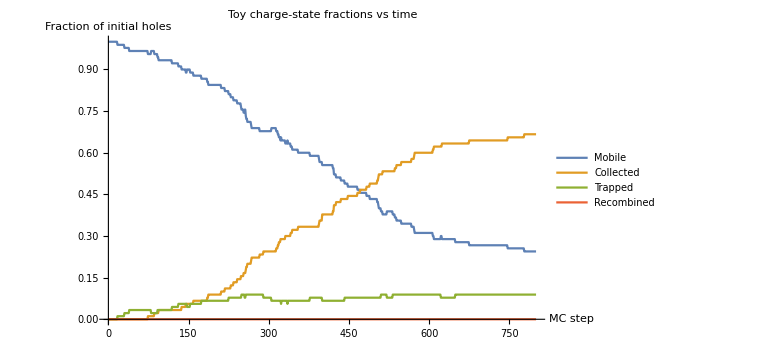

```mathematica
stateFractionByStep =
  Table[
    Module[{states = stateHistory[step]["Holes"][[All, "State"]], counts},
      counts = Counts[states];
      <|
        "Step" -> step,
        "Collected" -> Lookup[counts, "Collected", 0]/numberOfMobileHoles,
        "Trapped" -> Lookup[counts, "Trapped", 0]/numberOfMobileHoles,
        "Recombined" -> Lookup[counts, "Recombined", 0]/numberOfMobileHoles,
        "Mobile" -> Lookup[counts, "Mobile", 0]/numberOfMobileHoles
      |>
    ],
    {step, Sort[Keys[stateHistory]]}
  ];

ListLinePlot[
  Table[
    ({#["Step"], #[state]} & /@ stateFractionByStep),
    {state, {"Mobile", "Collected", "Trapped", "Recombined"}}
  ],
  PlotLegends -> {"Mobile", "Collected", "Trapped", "Recombined"},
  AxesLabel -> {"MC step", "Fraction of initial holes"},
  PlotLabel -> "Toy charge-state fractions vs time",
  PlotRange -> {0, 1},
  ImageSize -> Large
]
```

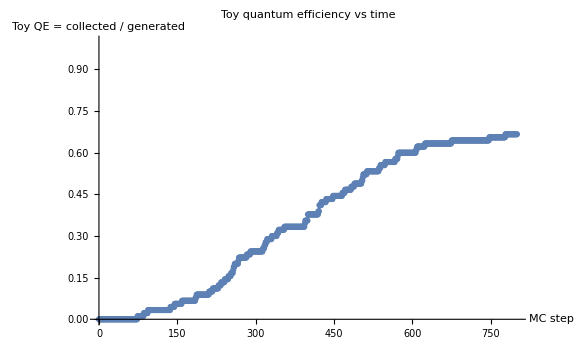

```mathematica
anodeLabels = Keys[stateHistory[First[storedSteps]]["Anodes"]];

anodeCountsByStep =
  AssociationMap[
    Function[step,
      Association @ KeyValueMap[
        Function[{anodeLabel, anodeData},
          anodeLabel -> anodeData["CollectedHoleCount"]
        ],
        stateHistory[step]["Anodes"]
      ]
    ],
    storedSteps
  ];

landingProbabilityByStep =
  AssociationMap[
    Function[step,
      Module[{counts, totalCollected},
        counts = anodeCountsByStep[step];
        totalCollected = Total[Values[counts]];

        AssociationMap[
          If[totalCollected == 0, 0, #/totalCollected] &,
          counts
        ]
      ]
    ],
    storedSteps
  ];

ListLinePlot[
  ({#, Total[Values[anodeCountsByStep[#]]]/numberOfMobileHoles} & /@ storedSteps),
  AxesLabel -> {"MC step", "Toy QE = collected / generated"},
  PlotLabel -> "Toy quantum efficiency vs time",
  PlotRange -> {0, 1},
  ImageSize -> Large,
  PlotMarkers -> Automatic
]
```

```mathematica
collectionStepByHole =
  AssociationMap[
    Function[holeID,
      Module[{firstCollected},
        firstCollected =
          SelectFirst[
            storedSteps,
            AnyTrue[
              stateHistory[#]["Holes"],
              Function[h,
                h["HoleID"] === holeID &&
                  h["State"] === "Collected"
              ]
            ] &
          ];

        If[MissingQ[firstCollected], Missing["NotCollected"], firstCollected]
      ]
    ],
    stateHistory[First[storedSteps]]["Holes"][[All, "HoleID"]]
  ];

collectedSteps =
  DeleteMissing[Values[collectionStepByHole]];

meanCollectionStep = Mean[collectedSteps];
medianCollectionStep = Median[collectedSteps];

{meanCollectionStep, medianCollectionStep}
```

{1135/3,749/2}

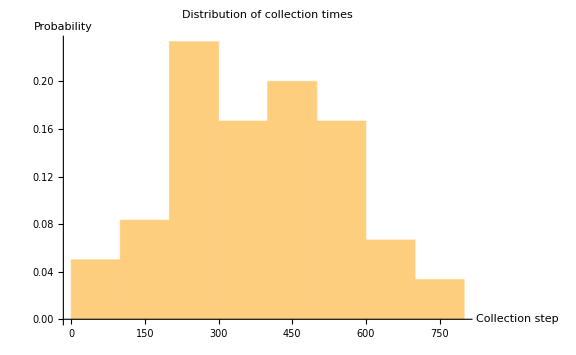

```mathematica
Histogram[
  collectedSteps,
  Automatic,
  "Probability",
  AxesLabel -> {"Collection step", "Probability"},
  PlotLabel -> "Distribution of collection times",
  ImageSize -> Large
]
```

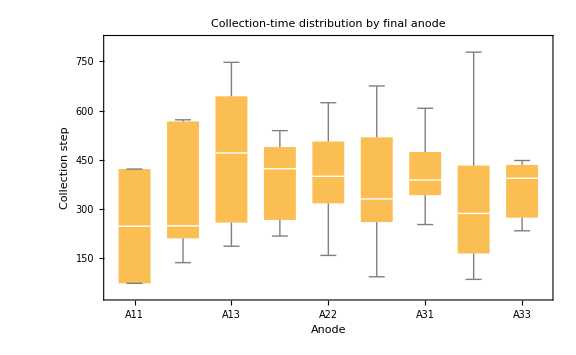

```mathematica
finalHoleRecords = stateHistory[numberOfTransportSteps]["Holes"];

collectionData =
  DeleteMissing[
    Table[
      Module[{holeID, finalAnode, collectionStep},
        holeID = h["HoleID"];
        finalAnode = h["CollectedByAnode"];
        collectionStep = collectionStepByHole[holeID];

        If[h["State"] === "Collected",
          <|"HoleID" -> holeID, "Anode" -> finalAnode, "CollectionStep" -> collectionStep|>,
          Missing["NotCollected"]
        ]
      ],
      {h, finalHoleRecords}
    ]
  ];

BoxWhiskerChart[
  Table[
    Select[collectionData, #["Anode"] === label &][[All, "CollectionStep"]],
    {label, anodeLabels}
  ],
  ChartLabels -> anodeLabels,
  AxesLabel -> {"Anode", "Collection step"},
  PlotLabel -> "Collection-time distribution by final anode",
  ImageSize -> Large
]
```

```mathematica
everTrappedQ[holeID_] :=
  AnyTrue[
    storedSteps,
    AnyTrue[
      stateHistory[#]["Holes"],
      Function[h, h["HoleID"] === holeID && h["State"] === "Trapped"]
    ] &
  ];

collectedHoleIDs =
  Select[finalHoleRecords, #["State"] === "Collected" &][[All, "HoleID"]];

fractionCollectedThatWereEverTrapped =
  Count[everTrappedQ /@ collectedHoleIDs, True]/Length[collectedHoleIDs]
```

1/15

```mathematica
summaryStats = <|
  "Initial holes" -> numberOfMobileHoles,
  "Collected holes" -> Lookup[finalStateCounts, "Collected", 0],
  "Toy QE" -> toyQE,
  "Recombined holes" -> Lookup[finalStateCounts, "Recombined", 0],
  "Loss fraction" -> lossFraction,
  "Trapped at final step" -> Lookup[finalStateCounts, "Trapped", 0],
  "Trapped fraction at final step" -> trappedFraction,
  "Mean collection step" -> meanCollectionStep,
  "Median collection step" -> medianCollectionStep
|>;

Dataset[summaryStats]
```

```mathematica
(*

Manipulate[
  plotHamiltonianLandscapeSlice[
    storedSteps[[stepIndex]],
    zSliceUm
  ],

  {{stepIndex, 1, "frame"}, 1, Length[storedSteps], 1,
    Appearance -> "Labeled"},

  {{zSliceUm, depletionThicknessUm/2, "z slice (um)"},
    0, depletionThicknessUm, latticeSpacingUm,
    Appearance -> "Labeled"},

  TrackedSymbols :> {stepIndex, zSliceUm},
  SynchronousUpdating -> False,
  ContinuousAction -> False
]

*)
```

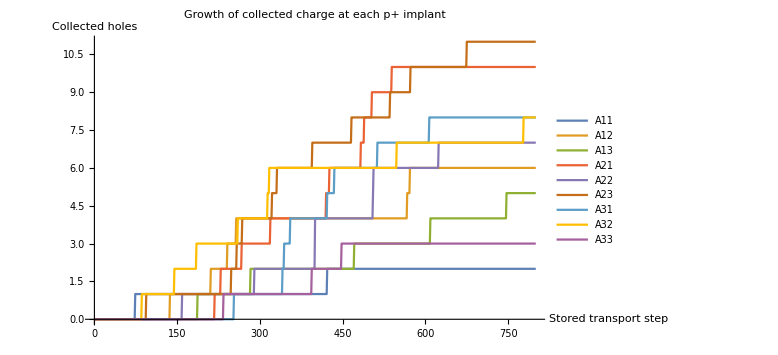
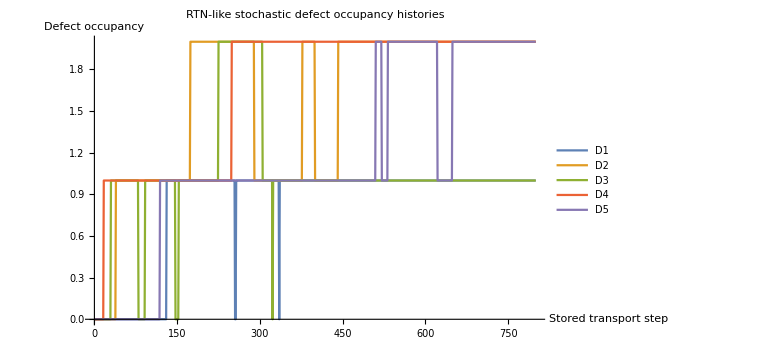
State counts

Anode collected-charge counts
Dataset[<>]
Defect occupancies

-Graphics-
-Graphics-

```mathematica
availableTransportSteps = Sort[Keys[stateHistory]];

nearestStoredStep[requestedStep_Integer] := Nearest[availableTransportSteps, requestedStep][[1]];

getStoredTransportState[requestedStep_Integer] := stateHistory[nearestStoredStep[requestedStep]];

(* Diagnostics replacement. *)
stateCountRows = Table[
  Join[
    <|"Step" -> step|>,
    Counts[stateHistory[step]["Holes"][[All, "State"]]]
  ],
  {step, availableTransportSteps}
];
stateCountDataset = Dataset[stateCountRows];

anodeLabels = Keys[stateHistory[First[availableTransportSteps]]["Anodes"]];
anodeCountRows = Table[
  Join[
    <|"Step" -> step|>,
    AssociationMap[
      stateHistory[step]["Anodes"][#]["CollectedHoleCount"] &,
      anodeLabels
    ]
  ],
  {step, availableTransportSteps}
];
anodeCountDataset = Dataset[anodeCountRows];

firstDefects = stateHistory[First[availableTransportSteps]]["Defects"];
defectIDs = firstDefects[[All, "DefectID"]];
defectLabels = ("D" <> ToString[#] &) /@ defectIDs;
defectOccupancyRows = Table[
  Join[
    <|"Step" -> step|>,
    AssociationThread[
      defectLabels,
      stateHistory[step]["Defects"][[All, "Occupancy"]]
    ]
  ],
  {step, availableTransportSteps}
];
defectOccupancyDataset = Dataset[defectOccupancyRows];

anodeChargeHistoryPlot = ListLinePlot[
  Table[
    ({# ["Step"], # [label]} & /@ anodeCountRows),
    {label, anodeLabels}
  ],
  PlotLegends -> anodeLabels,
  AxesLabel -> {"Stored transport step", "Collected holes"},
  PlotLabel -> "Growth of collected charge at each p+ implant",
  ImageSize -> Large
];

defectOccupancyHistoryPlot = ListLinePlot[
  Table[
    ({# ["Step"], # [label]} & /@ defectOccupancyRows),
    {label, defectLabels}
  ],
  PlotLegends -> defectLabels,
  AxesLabel -> {"Stored transport step", "Defect occupancy"},
  PlotLabel -> "RTN-like stochastic defect occupancy histories",
  ImageSize -> Large
];

Column[
  {
    Style["State counts", Bold, 14], stateCountDataset,
    Style["Anode collected-charge counts", Bold, 14], anodeCountDataset,
    Style["Defect occupancies", Bold, 14], defectOccupancyDataset,
    anodeChargeHistoryPlot,
    defectOccupancyHistoryPlot
  },
  Spacings -> 2
]
```